# Biaugmented Truncated Cube

### Author

Eric W. Weisstein
May 12, 2021

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polyhedra/BiaugmentedTruncatedCube.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/BiaugmentedTruncatedCube.html.

©2021 Wolfram Research, Inc. except for portions noted otherwise

## Solid

```mathematica
PolyhedronData["BiaugmentedTruncatedCube","Orientations"]
```

Missing[NotAvailable]

```mathematica
PolyhedronData["BiaugmentedTruncatedCube"]
```

-Graphics3D-

## Net

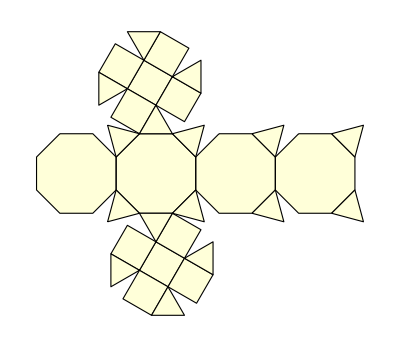

```mathematica
PolyhedronData["BiaugmentedTruncatedCube","Net"]
```

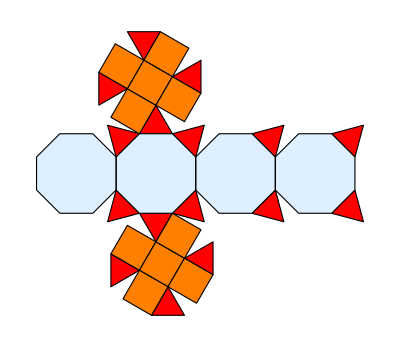

```mathematica
PolyhedronData["BiaugmentedTruncatedCube","Net","Colored"]
```

```mathematica
NetPrintout[PolyhedronData["BiaugmentedTruncatedCube","Polyhedron"],"SmallTriakisOctahedron.pdf"]
```

## Properties

```mathematica
<<MathWorld`PolyhedronOperations`
```

```mathematica
p=PolyhedronData[pname="BiaugmentedTruncatedCube","Polyhedron"]
```

Polyhedron[…]

### Centroid

```mathematica
Graphics3D[{AbsolutePointSize[10],
Point[{0,0,0}],{Blue,Point[PolyhedronData[pname,"Centroid"]]},Opacity[.2],PolyhedronData[pname,"GraphicsComplex"]}]
```

-Graphics3D-

```mathematica
PolyhedronData[pname,"Centroid"]
```

{0,0,0}

```mathematica
RegionCentroid[p]//FullSimplify
```

{0,0,0}

```mathematica
PolyhedronCentroid[p]
```

{0,0,0}

### Circumsphere

```mathematica
PolyhedronData[pname,"Circumsphere"]
```

Missing[NotApplicable]

```mathematica
Circumsphere[p]
```

Circumsphere::indep: Circumsphere does not exist for Polyhedron[{{-1/2,1/2 (1+√2),1/2 (1+√2)},{-1/2,1/2 (1+√2),1/2 (-1-√2)},{-1/2,1/2 (-1-√2),1/2 (1+√2)},{-1/2,1/2 (-1-√2),1/2 (-1-√2)},{0,-1/(√2),1/2 (1+2 √2)},{0,-1/(√2),1/2 (-1-2 √2)},{0,1/(√2),1/2 (1+2 √2)},{0,1/(√2),1/2 (-1-2 √2)},{1/2,1/2 (1+√2),1/2 (1+√2)},{1/2,1/2 (1+√2),1/2 (-1-√2)},«22»},{{3,32,31,4,12,23,24,11},{9,22,21,10,2,29,30,1},{17,24,23,18,20,21,22,19},«5»,{12,18,23},{21,20,10},«20»}].

Circumsphere[Polyhedron[…]]

```mathematica
sphere=MyCircumsphere[p]
```

{}

### Convex

```mathematica
ConvexPolyhedronQ[p]
```

True

### DihedralAngles

```mathematica
PolyhedronData[pname,"DihedralAngles"]//Tally
```

{{π/2,4},{ArcCos[-1/(√3)],16},{ArcCos[-√(2/3)],24},{ArcCos[(-2-√2)/(2 √3)],8},{(3 π)/4,8}}

```mathematica
DihedralAngles[p]//FullSimplify//Tally
```

{{π/2,4},{ArcSec[-√3],16},{ArcCos[-√(2/3)],24},{ArcCos[-(2+√2)/(2 √3)],8},{(3 π)/4,8}}

### EdgeLengths

```mathematica
PolyhedronData[pname,"EdgeLengths"]
```

{1}

```mathematica
PolyhedronData[pname,"Lines"]/.Line[l_]:>EuclideanDistance@@l//FullSimplify//Union
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2 (-1-√2)+1/2 (1+√2).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{1}

### Faces

### GeneralizedDiameter

```mathematica
PolyhedronData[pname,"GeneralizedDiameter"]
```

√(11+4 √2)

```mathematica
GeneralizedDiameter[p]//FullSimplify//Quiet
```

√(11+4 √2)

### Insphere

```mathematica
PolyhedronData[pname,"Insphere"]
```

Missing[NotApplicable]

```mathematica
Insphere[p]
```

Insphere::indep: Insphere does not exist for Polyhedron[{{-1/2,1/2 (1+√2),1/2 (1+√2)},{-1/2,1/2 (1+√2),1/2 (-1-√2)},{-1/2,1/2 (-1-√2),1/2 (1+√2)},{-1/2,1/2 (-1-√2),1/2 (-1-√2)},{0,-1/(√2),1/2 (1+2 √2)},{0,-1/(√2),1/2 (-1-2 √2)},{0,1/(√2),1/2 (1+2 √2)},{0,1/(√2),1/2 (-1-2 √2)},{1/2,1/2 (1+√2),1/2 (1+√2)},{1/2,1/2 (1+√2),1/2 (-1-√2)},«22»},{{3,32,31,4,12,23,24,11},{9,22,21,10,2,29,30,1},{17,24,23,18,20,21,22,19},«5»,{12,18,23},{21,20,10},«20»}].

Insphere[Polyhedron[…]]

```mathematica
MyInsphere[p]
```

{}

### InertiaTensor

```mathematica
PolyhedronData[pname,"InertiaTensor"]
```

{{19/36 (1+√2),0,0},{0,19/36 (1+√2),0},{0,0,1/18 (8+5 √2)}}

```mathematica
MomentOfInertia[p,{0,0,0}]/Volume[p]//FullSimplify//Timing
```

{2.89677,{{19/36 (1+√2),0,0},{0,19/36 (1+√2),0},{0,0,1/18 (8+5 √2)}}}

```mathematica
PolyhedronInertiaTensor[p]//FullSimplify//Timing
```

{2.63295,{{19/36 (1+√2),0,0},{0,19/36 (1+√2),0},{0,0,1/18 (8+5 √2)}}}

### MeanCylindricalRadius

```mathematica
NIntegrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.851324

```mathematica
(i=Integrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanCylindricalSquareRadius

```mathematica
NIntegrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

0.837282

```mathematica
(i=Integrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify)//Timing
```

{0.250729,1/18 (8+5 √2)}

```mathematica
N[i]
```

0.837282

### MeanSphericalRadius

```mathematica
NIntegrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

1.25036

```mathematica
(i=Integrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanSphericalSquareRadius

```mathematica
NIntegrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]
```

1.69281

```mathematica
(i=Integrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify)//Timing
```

{0.262431,3/4+(2 √2)/3}

```mathematica
N[i]
```

1.69281

### Midsphere

```mathematica
PolyhedronData[pname,"Midsphere"]
```

Missing[NotApplicable]

```mathematica
Midsphere[p]
```

{}

### SurfaceArea

```mathematica
PolyhedronData[pname,"SurfaceArea"]
```

18+8 √2+4 √3

```mathematica
SurfaceArea[p]//FullSimplify
```

18+8 √2+4 √3

```mathematica
Total[Area/@PolyhedronData[pname,"Polygons"]]//FullSimplify
```

18+8 √2+4 √3

### VertexSubsetHulls

```mathematica
PolyhedronData[pname,"VertexSubsetHulls"]
```

{AugmentedTruncatedCube→{{1,2,3,4,5,7,9,10,11,12,13,15,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32},{1,2,3,4,6,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}},BiaugmentedTruncatedCube→{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}},SquareCupola→{{1,3,5,7,9,11,13,15,17,19,25,27},{2,4,6,8,10,12,14,16,18,20,26,28}},TruncatedCube→{{1,2,3,4,9,10,11,12,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}}}

#### Platonic

```mathematica
(h=VertexSubsetHulls[p,"Platonic","Skip"->{}])//Timing
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedra from octahedra...

Finding icosahedra by building up from equilateral triangles...

{0.1261,{}}

### Volume

```mathematica
PolyhedronData[pname,"Volume"]
```

9+6 √2

```mathematica
Volume[p]//FullSimplify
```

9+6 √2

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//FullSimplify
```

9+6 √2

## Perspective projections

```mathematica
Manipulate[PolyhedronProjectionGraph[PolyhedronData["Cuboctahedron","Polyhedron"],{a,b,c}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

### XXX

```mathematica
PolyhedronProjectionGraph[PolyhedronData["DuererSolid","Polyhedron"],]
```